## 3.029 Spring 2022 Code Show & Tell 01 - 02/17/2022

## Mysterious beating heart patterns

Based on Wolfram community post:
 https://community.wolfram.com/groups/-/m/t/2471154

Introduction to Elementary CAs:

https://gvarnavides.com/generative-art-workshop-website/docs/01.27-Thursday/elementary-cellular-automata

Talked a bunch on the board..

Let’s investigate a famous 2D CA - Conway’s Game of Life

https://en.wikipedia.org/wiki/Conway%27s_Game_of_Life

We start with an {50,50} board of random integers b/w 0 and 1 (our two states “off” or “on”)

```mathematica
board=RandomInteger[1,{50,50}];
ArrayPlot[board,Frame->All]
```

-Graphics-

And we evolve it as follows

```mathematica
frames=ArrayPlot/@CellularAutomaton[gameOfLife,board,500];
Multicolumn[frames[[1;;-2;;25]],5,Appearance->"Horizontal"]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Let’s break this down

Starting with the aptly-named CellularAutomaton command

```mathematica
?CellularAutomaton
```

Notice there are multiple ways we can call this function

This is similar to “Multiple Dispatch” or “Function Overload”

Aside on Multiple Dispatch / Function Overload

```mathematica
function[a_,b_]:=a+b
```

```mathematica
function[3,4]
```

7

```mathematica
function[{a_,b_}]:=a b
```

```mathematica
function[{3,4}]
```

12

```mathematica
?function
```

Default CellularAutomaton[n]

1D Elementary CA w/ two states (on and off), with first-nearest neighbors

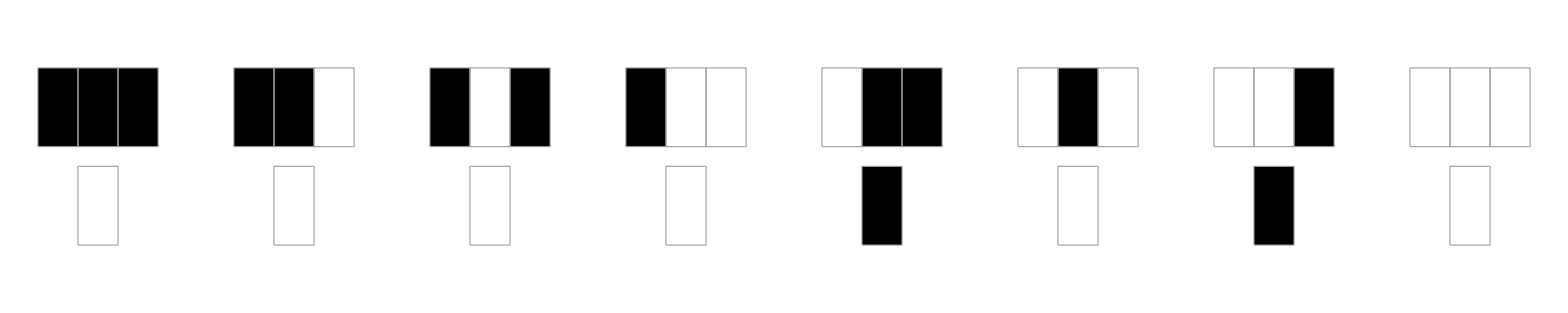

```mathematica
CellularAutomaton[10]//RulePlot
```

CellularAutomaton[{n,k}], where k is the number of states for each cell, e.g. here 3

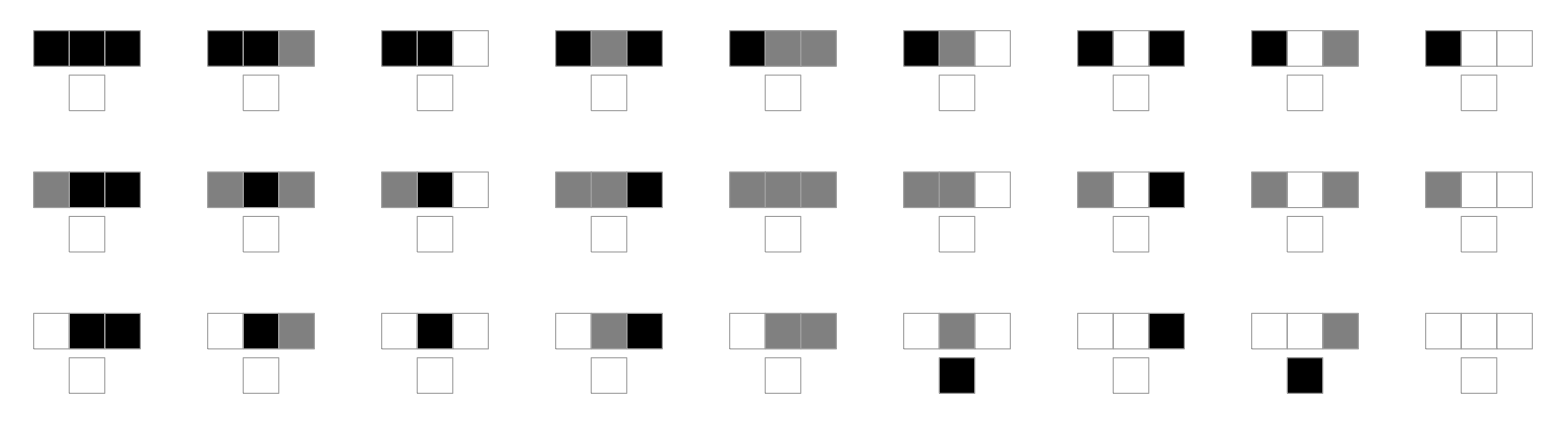

```mathematica
CellularAutomaton[{60,3}]//RulePlot
```

CellularAutomaton[{n,k,r}], where r is the range specification (i.e. how many nearest-neighbors to include)

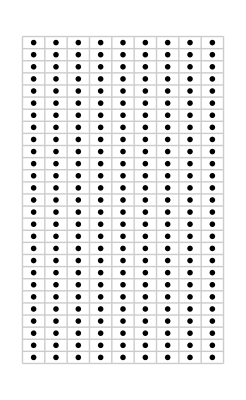

```mathematica
CellularAutomaton[{60,3,2}]//RulePlot
```

CellularAutomaton[{n,{k,{weights..}},r}], where weights is a list of how to weigh each neighbor

Notice that by specifying {rx,ry} - we defined a 2D neighborhood

```mathematica
gameOfLife={
224,
{2,{{2,2,2},{2,1,2},{2,2,2}}},
{1,1}
};
```

Let’s verify using

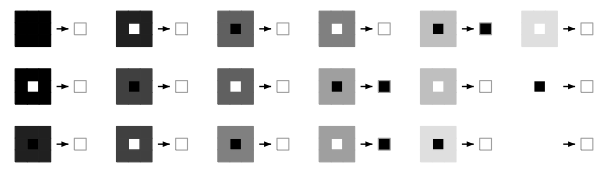

```mathematica
CellularAutomaton[gameOfLife]//RulePlot
```

```mathematica
board=RandomInteger[1,{50,50}];
frames=ArrayPlot/@CellularAutomaton[gameOfLife,board,500];
```

More on Game of Life

https://en.wikipedia.org/wiki/Conway%27s_Game_of_Life

```mathematica
ListAnimate[frames]
```

Back to Blog-post

Starts with an example of a totalistic CA in 1D

Let’s check it’s indeed totalistic

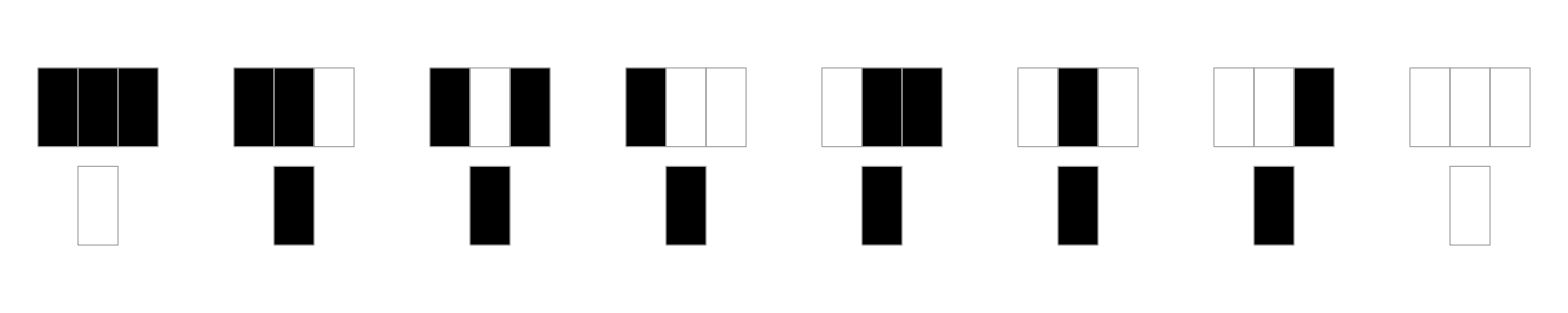

```mathematica
CellularAutomaton[126]//RulePlot
```

SeedRandom

Ensures each time we call RandomInteger below - we get the same result

```mathematica
?SeedRandom
```

```mathematica
SeedRandom["PlotFun!"];
Image[CellularAutomaton[126,RandomInteger[1,100],100],ImageSize->400]
```

-Graphics-

The blog goes on to suggest looking at a heart-shaped neighborhood we might be able to get heart-patterns

```mathematica
HeartNeighborhood={{-1,1},{1,1},{-1,0},{1,0},{0,0},{0,-1}};
Graphics[Rectangle/@HeartNeighborhood,ImageSize->50]
```

-Graphics-

Note this is using yet another form

CellularAutomaton[{n,k,{{off_1},{off_2},…,{off_s}}} ] where one explicitly lists the neighbors (here the heart-shaped ones)

```mathematica
CAFirstArg[code_,transform_:Identity]:={code,4,transform/@HeartNeighborhood}
```

RulePlot does not seem to work on this form, odd..

```mathematica
RulePlot[CellularAutomaton[CAFirstArg[127594045460,Reverse]]]
```

RulePlot[CellularAutomaton[{127594045460,4,{{1,-1},{1,1},{0,-1},{0,1},{0,0},{-1,0}}}]]

Here this is a rather brute-force approach, to find the CAs which return a valid image

Let’s dissect this code

```mathematica
SearchCA[ntime_]:=Quiet[With[{RandDat=DeleteCases[Rule[Show[#,ImageSize->200]&@Image[CellularAutomaton[CAFirstArg[#,Reverse],{{{1}},0},{{{ntime}}}]/3],#]&/@RandomInteger[{0,4^19-1},100],Rule[Image[{}],_]]},

Select[RandDat,10<ImageDimensions[#[[1]]][[1]]<2 ntime&]]]
```

Quiet suppressers errors

Usually a bad idea

Here, this is intentional - as the author wants to leave Image[{}] unevaluated

A better approach would have been to only silence that particular message using

```mathematica
Quiet[Image[{}],Image::imgarray]
```

Image[{}]

The main operation is done w/ DeleteCases

which takes an expression, and then deletes elements which match a pattern

Here, the author is making a list of elements of the form Image[CA]->CA-rule-number

And Deleting elements which match the pattern Image[{}] -> _

I.e. CAs which returned empty

```mathematica
DeleteCases[Range[10],a_/;a<5]
```

{5,6,7,8,9,10}

```mathematica
?Rule
```

```mathematica
{1,2,4,5,6}/. 4->5
```

{1,2,5,5,6}

```mathematica
Rule[4,5]
```

4→5

Note that the second argument here in CellularAutomaton

which is the initial condition

is given in a special syntax to suggest a single “on” pixel in a sea of “off” pixels (whose dimensions are allowed to expand depending on how many time steps we take)

```mathematica
CellularAutomaton[CAFirstArg[205921493049,Reverse],{{{1}},0},{{{25}}}]
```

{}

```mathematica
SearchCA[25]
```

{-Graphics-→90903691544,-Graphics-→145380365796,-Graphics-→126303231164,-Graphics-→109861546536}

Finally, the author wants a convenient way to select the CAs they like

So they use a ResourceFunction called InteractiveListSelector to do that

```mathematica
[SearchCA[25]]
```

{214125219748,7700198328}

Note that Resource Functions https://resources.wolframcloud.com/FunctionRepository/ are user-contributed functions which are:

a) accessible from the WolframLanguage as built-in functions

b) well-documented!

```mathematica
ResourceFunction["InteractiveListSelector"]
```